```mathematica
Clear["Global`*"]
```

### Calculating displacements correlation for 2 connected particles in 2D (1D x-link). ω0=k/γ

```mathematica
A=1/γ({{-k1-k12, 0, k12, 0}, {0, -k1, 0, 0}, {k12, 0, -k2-k12, 0}, {0, 0, 0, -k2}});
eigsys=Eigensystem[A];
Um1= eigsys[[2]];
λs=eigsys[[1]];
gRule=g->√(k1^2+4 k12^2-2 k1 k2+k2^2);
Um1=Um1/.((g/.gRule)->g);
λs=λs/.((g/.gRule)->g);

U=Inverse[Um1];
(*λ=-2 k12/γ;*)
b[1]=Transpose[{{√(2 D1),0,0,0}}];
b[2]=Transpose[{{0, √(2D1),0,0}}];
b[3]=Transpose[{{0, 0,√(2D2),0}}];
b[4]=Transpose[{{0, 0,0,√(2D2)}}];
R0=Transpose[{{R01,R02,R03,R04}}];
a =L/γ ({{-k12}, {0}, {k2+k12}, {0}});
Um1//MatrixForm
λs
Print["Check eigenvectors:",
Simplify[U.DiagonalMatrix[λs].Um1-A]/.gRule//MatrixForm]
λsDummy=Table[λ[i],{i,1,4}];
```

(0 | 1 | 0 | 0
0 | 0 | 0 | 1
-(g+k1-k2)/(2 k12) | 0 | 1 | 0
-(-g+k1-k2)/(2 k12) | 0 | 1 | 0)

{-k1/γ,-k2/γ,(-g-k1-2 k12-k2)/(2 γ),(g-k1-2 k12-k2)/(2 γ)}

Check eigenvectors:(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### Stochastic part of the displacement J[λ, n] = ∫_0^t_n ⅇ^(λ(t_n-s))ⅆW

```mathematica
f1 = Sum[p[i] U.DiagonalMatrix[Map[J[#,n]&,λsDummy]].Um1.b[i],{i,1,4}];
ξn=RnStochastic=(f1/.n->n+1)-f1;
```

#### Construct the power spectrum. Decorrelate different stochastic noise processes

```mathematica
pRule = {p[_]^2:>1,p[i_] p[j_] /;i≠j:> 0};
RnStochasticImSquared=Expand[RnStochastic*(RnStochastic/.ⅈ->-ⅈ)]/.pRule//Simplify;
```

### Calculate the variances of the individual χ^2 for the Real component

```mathematica
U.DiagonalMatrix[Map[J[#]&,λsDummy]].Um1//MatrixForm
```

(((g+k1-k2) J[λ[3]])/(2 g)-((-g+k1-k2) J[λ[4]])/(2 g) | 0 | -(k12 J[λ[3]])/g+(k12 J[λ[4]])/g | 0
0 | J[λ[1]] | 0 | 0
((-g+k1-k2) (g+k1-k2) J[λ[3]])/(4 g k12)-((-g+k1-k2) (g+k1-k2) J[λ[4]])/(4 g k12) | 0 | -((-g+k1-k2) J[λ[3]])/(2 g)+((g+k1-k2) J[λ[4]])/(2 g) | 0
0 | 0 | 0 | J[λ[2]])

```mathematica
iRule=i->3;
term=U.DiagonalMatrix[Map[J[#]&,λs]].Um1.b[i];
term/.iRule//MatrixForm
```

(√2 √D2 (-(k12 J[(-g-k1-2 k12-k2)/(2 γ)])/g+(k12 J[(g-k1-2 k12-k2)/(2 γ)])/g)
0
√2 √D2 (-((-g+k1-k2) J[(-g-k1-2 k12-k2)/(2 γ)])/(2 g)+((g+k1-k2) J[(g-k1-2 k12-k2)/(2 γ)])/(2 g))
0)

### Substitute the integrals product with Fourier images results. Only use the ~M terms. For k!=0. My calculations show that the variance of the real part is the same as that of the imaginary part, and they are not correlated

```mathematica
JReImage={J[λ1_]^2/;λ1===0:>M dt^3/2,
J[λ1_]^2/;λ1=!=0:>(((M dt^2)/(-2 λ1))(((1-c1^2)(1-Cos[2π k/M]))/(1+c1^2-2c1 Cos[2 π k /M]))/.c1->Exp[λ1 dt]),
J[λ1_]J[λ2_]/;(λ1=!=λ2):>(((M dt^2)/(-(λ1+λ2)))(((1-c1 c2)(1+c1 c2 -(c1+c2)Cos[2π k/M])(1-Cos[2 π k/M]))/((1+c1^2-2c1 Cos[2 π k /M])(1+c2^2-2c2 Cos[2 π k /M])))/.{c1->Exp[λ1 dt],c2->Exp[λ2 dt]})
}
termSquared=(term/.iRule)^2//MatrixForm
(*termSquared/.JReImage//FullSimplify*)
```

{J[λ1_]^2/;λ1===0:>(M dt^3)/2,J[λ1_]^2/;λ1=!=0:>(-((M dt^2) ((1-c1^2) (1-Cos[(2 π k)/M])))/((2 λ1) (1+c1^2-2 c1 Cos[(2 π k)/M]))/.c1→Exp[λ1 dt]),J[λ1_] J[λ2_]/;λ1=!=λ2:>(-((M dt^2) ((1-c1 c2) (1+c1 c2-(c1+c2) Cos[(2 π k)/M]) (1-Cos[(2 π k)/M])))/((λ1+λ2) ((1+c1^2-2 c1 Cos[(2 π k)/M]) (1+c2^2-2 c2 Cos[(2 π k)/M])))/.{c1→Exp[λ1 dt],c2→Exp[λ2 dt]})}

(2 D2 (-(k12 J[(-g-k1-2 k12-k2)/(2 γ)])/g+(k12 J[(g-k1-2 k12-k2)/(2 γ)])/g)^2
0
2 D2 (-((-g+k1-k2) J[(-g-k1-2 k12-k2)/(2 γ)])/(2 g)+((g+k1-k2) J[(g-k1-2 k12-k2)/(2 γ)])/(2 g))^2
0)

```mathematica
(combinedMean=FullSimplify[Sum[(term)^2,{i,1,4}]])//MatrixForm;
(combinedMean=Collect[combinedMean,{J[-(-g+k1+2 k12+k2)/(2 γ)],J[-(g+k1+2 k12+k2)/(2 γ)]}])//MatrixForm
```

(((4 D2 k12^2+D1 (g-k1+k2)^2) J[-(-g+k1+2 k12+k2)/(2 γ)]^2)/(2 g^2)+((-8 D2 k12^2+2 D1 (g+k1-k2) (g-k1+k2)) J[-(-g+k1+2 k12+k2)/(2 γ)] J[-(g+k1+2 k12+k2)/(2 γ)])/(2 g^2)+((4 D2 k12^2+D1 (g+k1-k2)^2) J[-(g+k1+2 k12+k2)/(2 γ)]^2)/(2 g^2)
2 D1 J[-k1/γ]^2
((4 D2 k12^2 (g+k1-k2)^2+D1 (g+k1-k2)^2 (g-k1+k2)^2) J[-(-g+k1+2 k12+k2)/(2 γ)]^2)/(8 g^2 k12^2)+((8 D2 k12^2 (g+k1-k2) (g-k1+k2)-2 D1 (g+k1-k2)^2 (g-k1+k2)^2) J[-(-g+k1+2 k12+k2)/(2 γ)] J[-(g+k1+2 k12+k2)/(2 γ)])/(8 g^2 k12^2)+((4 D2 k12^2 (g-k1+k2)^2+D1 (g+k1-k2)^2 (g-k1+k2)^2) J[-(g+k1+2 k12+k2)/(2 γ)]^2)/(8 g^2 k12^2)
2 D2 J[-k2/γ]^2)

```mathematica
(meanPowerSpectrum=2*combinedMean/(M dt)/.JReImage//Simplify)//MatrixForm
```

((2 dt γ (((-1+ⅇ^((dt (-g+k1+2 k12+k2))/γ)) (4 D2 k12^2+D1 (g-k1+k2)^2))/((-g+k1+2 k12+k2) (1+ⅇ^((dt (-g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (-g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]))+((-1+ⅇ^((dt (g+k1+2 k12+k2))/γ)) (4 D2 k12^2+D1 (g+k1-k2)^2))/((g+k1+2 k12+k2) (1+ⅇ^((dt (g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]))-(2 (-1+ⅇ^((dt (k1+2 k12+k2))/γ)) (4 D2 k12^2+D1 (-g^2+(k1-k2)^2)) (1+ⅇ^((dt (k1+2 k12+k2))/γ)-(ⅇ^((dt (-g+k1+2 k12+k2))/(2 γ))+ⅇ^((dt (g+k1+2 k12+k2))/(2 γ))) Cos[(2 k π)/M]))/((k1+2 k12+k2) (1+ⅇ^((dt (-g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (-g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]) (1+ⅇ^((dt (g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]))) Sin[(k π)/M]^2)/g^2
(4 D1 dt (-1+ⅇ^((2 dt k1)/γ)) γ Sin[(k π)/M]^2)/(k1 (1+ⅇ^((2 dt k1)/γ)-2 ⅇ^((dt k1)/γ) Cos[(2 k π)/M]))
(dt γ (((-1+ⅇ^((dt (-g+k1+2 k12+k2))/γ)) (g+k1-k2)^2 (4 D2 k12^2+D1 (g-k1+k2)^2))/((-g+k1+2 k12+k2) (1+ⅇ^((dt (-g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (-g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]))+((-1+ⅇ^((dt (g+k1+2 k12+k2))/γ)) (4 D2 k12^2+D1 (g+k1-k2)^2) (g-k1+k2)^2)/((g+k1+2 k12+k2) (1+ⅇ^((dt (g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]))-(2 (-1+ⅇ^((dt (k1+2 k12+k2))/γ)) (4 D2 k12^2+D1 (-g^2+(k1-k2)^2)) (-g^2+(k1-k2)^2) (1+ⅇ^((dt (k1+2 k12+k2))/γ)-(ⅇ^((dt (-g+k1+2 k12+k2))/(2 γ))+ⅇ^((dt (g+k1+2 k12+k2))/(2 γ))) Cos[(2 k π)/M]))/((k1+2 k12+k2) (1+ⅇ^((dt (-g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (-g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]) (1+ⅇ^((dt (g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]))) Sin[(k π)/M]^2)/(2 g^2 k12^2)
(4 D2 dt (-1+ⅇ^((2 dt k2)/γ)) γ Sin[(k π)/M]^2)/(k2 (1+ⅇ^((2 dt k2)/γ)-2 ⅇ^((dt k2)/γ) Cos[(2 k π)/M])))

### After all, I am only really interested in the x component of the 1st particle, because the system is symmetric, and y components are simple

```mathematica
meanPowerSpectrum[[1,1]]
```

1/g^2 2 dt γ (((-1+ⅇ^((dt (-g+k1+2 k12+k2))/γ)) (4 D2 k12^2+D1 (g-k1+k2)^2))/((-g+k1+2 k12+k2) (1+ⅇ^((dt (-g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (-g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]))+((-1+ⅇ^((dt (g+k1+2 k12+k2))/γ)) (4 D2 k12^2+D1 (g+k1-k2)^2))/((g+k1+2 k12+k2) (1+ⅇ^((dt (g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]))-(2 (-1+ⅇ^((dt (k1+2 k12+k2))/γ)) (4 D2 k12^2+D1 (-g^2+(k1-k2)^2)) (1+ⅇ^((dt (k1+2 k12+k2))/γ)-(ⅇ^((dt (-g+k1+2 k12+k2))/(2 γ))+ⅇ^((dt (g+k1+2 k12+k2))/(2 γ))) Cos[(2 k π)/M]))/((k1+2 k12+k2) (1+ⅇ^((dt (-g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (-g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]) (1+ⅇ^((dt (g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]))) Sin[(k π)/M]^2

```mathematica
Collect[meanPowerSpectrum[[1,1]],D2]
```

1/g^2 2 D2 dt γ ((4 (-1+ⅇ^((dt (-g+k1+2 k12+k2))/γ)) k12^2)/((-g+k1+2 k12+k2) (1+ⅇ^((dt (-g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (-g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]))+(4 (-1+ⅇ^((dt (g+k1+2 k12+k2))/γ)) k12^2)/((g+k1+2 k12+k2) (1+ⅇ^((dt (g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]))-(8 (-1+ⅇ^((dt (k1+2 k12+k2))/γ)) k12^2 (1+ⅇ^((dt (k1+2 k12+k2))/γ)-(ⅇ^((dt (-g+k1+2 k12+k2))/(2 γ))+ⅇ^((dt (g+k1+2 k12+k2))/(2 γ))) Cos[(2 k π)/M]))/((k1+2 k12+k2) (1+ⅇ^((dt (-g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (-g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]) (1+ⅇ^((dt (g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]))) Sin[(k π)/M]^2+1/g^2 2 dt γ ((D1 (-1+ⅇ^((dt (-g+k1+2 k12+k2))/γ)) (g-k1+k2)^2)/((-g+k1+2 k12+k2) (1+ⅇ^((dt (-g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (-g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]))+(D1 (-1+ⅇ^((dt (g+k1+2 k12+k2))/γ)) (g+k1-k2)^2)/((g+k1+2 k12+k2) (1+ⅇ^((dt (g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]))-(2 D1 (-1+ⅇ^((dt (k1+2 k12+k2))/γ)) (-g^2+(k1-k2)^2) (1+ⅇ^((dt (k1+2 k12+k2))/γ)-(ⅇ^((dt (-g+k1+2 k12+k2))/(2 γ))+ⅇ^((dt (g+k1+2 k12+k2))/(2 γ))) Cos[(2 k π)/M]))/((k1+2 k12+k2) (1+ⅇ^((dt (-g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (-g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]) (1+ⅇ^((dt (g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]))) Sin[(k π)/M]^2

```mathematica
g2Rule = g^2->(g^2/.gRule)
Coefficient[meanPowerSpectrum[[1,1]],g,2]
FullSimplify[(g-k1+k2)^2/.gRule,Assumptions->{k1>0,k2>0,k12>0}]
Collect[meanPowerSpectrum[[1,1]],g]/.g2Rule//Simplify
```

g^2→k1^2+4 k12^2-2 k1 k2+k2^2

0

(-k1+√(4 k12^2+(k1-k2)^2)+k2)^2

1/g^2 2 dt γ (((-1+ⅇ^((dt (-g+k1+2 k12+k2))/γ)) (4 D2 k12^2+D1 (g-k1+k2)^2))/((-g+k1+2 k12+k2) (1+ⅇ^((dt (-g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (-g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]))+((-1+ⅇ^((dt (g+k1+2 k12+k2))/γ)) (4 D2 k12^2+D1 (g+k1-k2)^2))/((g+k1+2 k12+k2) (1+ⅇ^((dt (g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]))+(8 (D1-D2) (-1+ⅇ^((dt (k1+2 k12+k2))/γ)) k12^2 (1+ⅇ^((dt (k1+2 k12+k2))/γ)-(ⅇ^((dt (-g+k1+2 k12+k2))/(2 γ))+ⅇ^((dt (g+k1+2 k12+k2))/(2 γ))) Cos[(2 k π)/M]))/((k1+2 k12+k2) (1+ⅇ^((dt (-g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (-g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]) (1+ⅇ^((dt (g+k1+2 k12+k2))/γ)-2 ⅇ^((dt (g+k1+2 k12+k2))/(2 γ)) Cos[(2 k π)/M]))) Sin[(k π)/M]^2

```mathematica
meanPowerSpectrum[[1,1]]//FullSimplify
```

$Aborted

### Calculate the numerical values for the first component

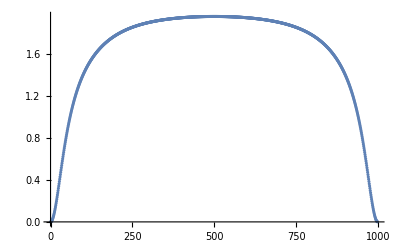

```mathematica
values={D1->1,D2->3,k12->1,k1->1,k2->1,γ->1,dt->0.3,M->999};
num1=Table[{k,meanPowerSpectrum[[1,1]]/(D1 dt^2)/.gRule/.values},{k,0,M-1/.values}];
ListPlot[num1,AxesOrigin->{0,0}]
```

### Get the image of the deterministic part. Keep only terms for L[0], because everything else is ~O(1)

```mathematica
detImage=U.DiagonalMatrix[Map[K[#]&,λs]].Um1.R0+U.DiagonalMatrix[Map[L[#]&,λs]].Um1.a;
LKImages={K[λ1_]/;λ1===0:>0,
K[λ1_]/;λ1=!=0:>(dt (1-Exp[M λ1 dt])(Exp[λ1dt]-1))/(1-Exp[λ1 dt-2 π ⅈ k /M]),
L[λ1_]/;λ1===0:>M dt^2 δ[k],
L[λ1_]/;λ1=!=0:>(dt (1-Exp[M λ1 dt])(Exp[λ1dt]-1))/(1-Exp[λ1 dt-2 π ⅈ k /M])/λ1
};
detImage/.LKImages//Simplify
%//MatrixForm
```

{{(dt ⅇ^((2 ⅈ k π)/M-(dt k2 (-1+M))/γ) (-1+ⅇ^((dt k2 M)/γ)) (-1+ⅇ^λ1dt) (k12 L+k2 R01))/((-1+ⅇ^((2 ⅈ k π)/M+(dt k2)/γ)) k2)},{(dt (1-ⅇ^((dt (-k1-2 k12-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) M)/(2 γ))) (-1+ⅇ^λ1dt) R02)/(1-ⅇ^(-(2 ⅈ k π)/M+(dt (-k1-2 k12-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(2 γ)))},{(dt (1-ⅇ^λ1dt) (-(k12+k2) (2 (1-ⅇ^(-(2 ⅈ k π)/M-(dt k1)/γ)) (1-ⅇ^(-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) M)/(2 γ))) k1 (k1-k2-√(k1^2+4 k12^2-2 k1 k2+k2^2))-(1-ⅇ^(-(2 ⅈ k π)/M-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(2 γ))) (1-ⅇ^(-(dt k1 M)/γ)) (k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2))) L+k1 (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) ((1-ⅇ^(-(2 ⅈ k π)/M-(dt k1)/γ)) (1-ⅇ^(-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) M)/(2 γ))) (k1-k2-√(k1^2+4 k12^2-2 k1 k2+k2^2))-(1-ⅇ^(-(2 ⅈ k π)/M-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(2 γ))) (1-ⅇ^(-(dt k1 M)/γ)) (k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2))) R03+((1-ⅇ^(-(2 ⅈ k π)/M-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(2 γ))) (1-ⅇ^(-(dt k1 M)/γ))-(1-ⅇ^(-(2 ⅈ k π)/M-(dt k1)/γ)) (1-ⅇ^(-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) M)/(2 γ)))) k1 (k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) R04))/(2 (1-ⅇ^(-(2 ⅈ k π)/M-(dt k1)/γ)) (1-ⅇ^(-(2 ⅈ k π)/M-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(2 γ))) k1 √(k1^2+4 k12^2-2 k1 k2+k2^2) (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))},{(dt (1-ⅇ^λ1dt) (-(k12+k2) (k1-k2-√(k1^2+4 k12^2-2 k1 k2+k2^2)) (2 (1-ⅇ^(-(2 ⅈ k π)/M-(dt k1)/γ)) (1-ⅇ^(-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) M)/(2 γ))) k1-(1-ⅇ^(-(2 ⅈ k π)/M-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(2 γ))) (1-ⅇ^(-(dt k1 M)/γ)) (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2))) L-((1-ⅇ^(-(2 ⅈ k π)/M-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(2 γ))) (1-ⅇ^(-(dt k1 M)/γ))-(1-ⅇ^(-(2 ⅈ k π)/M-(dt k1)/γ)) (1-ⅇ^(-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) M)/(2 γ)))) k1 (k1-k2-√(k1^2+4 k12^2-2 k1 k2+k2^2)) (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) R03+k1 (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) ((1-ⅇ^(-(2 ⅈ k π)/M-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(2 γ))) (1-ⅇ^(-(dt k1 M)/γ)) (k1-k2-√(k1^2+4 k12^2-2 k1 k2+k2^2))-(1-ⅇ^(-(2 ⅈ k π)/M-(dt k1)/γ)) (1-ⅇ^(-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) M)/(2 γ))) (k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2))) R04))/(2 (1-ⅇ^(-(2 ⅈ k π)/M-(dt k1)/γ)) (1-ⅇ^(-(2 ⅈ k π)/M-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(2 γ))) k1 √(k1^2+4 k12^2-2 k1 k2+k2^2) (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))}}

((dt ⅇ^((2 ⅈ k π)/M-(dt k2 (-1+M))/γ) (-1+ⅇ^((dt k2 M)/γ)) (-1+ⅇ^λ1dt) (k12 L+k2 R01))/((-1+ⅇ^((2 ⅈ k π)/M+(dt k2)/γ)) k2)
(dt (1-ⅇ^((dt (-k1-2 k12-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) M)/(2 γ))) (-1+ⅇ^λ1dt) R02)/(1-ⅇ^(-(2 ⅈ k π)/M+(dt (-k1-2 k12-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(2 γ)))
(dt (1-ⅇ^λ1dt) (-(k12+k2) (2 (1-ⅇ^(-(2 ⅈ k π)/M-(dt k1)/γ)) (1-ⅇ^(-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) M)/(2 γ))) k1 (k1-k2-√(k1^2+4 k12^2-2 k1 k2+k2^2))-(1-ⅇ^(-(2 ⅈ k π)/M-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(2 γ))) (1-ⅇ^(-(dt k1 M)/γ)) (k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2))) L+k1 (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) ((1-ⅇ^(-(2 ⅈ k π)/M-(dt k1)/γ)) (1-ⅇ^(-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) M)/(2 γ))) (k1-k2-√(k1^2+4 k12^2-2 k1 k2+k2^2))-(1-ⅇ^(-(2 ⅈ k π)/M-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(2 γ))) (1-ⅇ^(-(dt k1 M)/γ)) (k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2))) R03+((1-ⅇ^(-(2 ⅈ k π)/M-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(2 γ))) (1-ⅇ^(-(dt k1 M)/γ))-(1-ⅇ^(-(2 ⅈ k π)/M-(dt k1)/γ)) (1-ⅇ^(-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) M)/(2 γ)))) k1 (k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) R04))/(2 (1-ⅇ^(-(2 ⅈ k π)/M-(dt k1)/γ)) (1-ⅇ^(-(2 ⅈ k π)/M-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(2 γ))) k1 √(k1^2+4 k12^2-2 k1 k2+k2^2) (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))
(dt (1-ⅇ^λ1dt) (-(k12+k2) (k1-k2-√(k1^2+4 k12^2-2 k1 k2+k2^2)) (2 (1-ⅇ^(-(2 ⅈ k π)/M-(dt k1)/γ)) (1-ⅇ^(-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) M)/(2 γ))) k1-(1-ⅇ^(-(2 ⅈ k π)/M-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(2 γ))) (1-ⅇ^(-(dt k1 M)/γ)) (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2))) L-((1-ⅇ^(-(2 ⅈ k π)/M-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(2 γ))) (1-ⅇ^(-(dt k1 M)/γ))-(1-ⅇ^(-(2 ⅈ k π)/M-(dt k1)/γ)) (1-ⅇ^(-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) M)/(2 γ)))) k1 (k1-k2-√(k1^2+4 k12^2-2 k1 k2+k2^2)) (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) R03+k1 (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) ((1-ⅇ^(-(2 ⅈ k π)/M-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(2 γ))) (1-ⅇ^(-(dt k1 M)/γ)) (k1-k2-√(k1^2+4 k12^2-2 k1 k2+k2^2))-(1-ⅇ^(-(2 ⅈ k π)/M-(dt k1)/γ)) (1-ⅇ^(-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) M)/(2 γ))) (k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2))) R04))/(2 (1-ⅇ^(-(2 ⅈ k π)/M-(dt k1)/γ)) (1-ⅇ^(-(2 ⅈ k π)/M-(dt (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(2 γ))) k1 √(k1^2+4 k12^2-2 k1 k2+k2^2) (k1+2 k12+k2+√(k1^2+4 k12^2-2 k1 k2+k2^2))))

### Conclusion: the deterministic part does not have terms of order ~M, and is absent at all for the correct initial conditions

```mathematica
Clear[K]
```

```mathematica
K
```

K

```mathematica
K[1]
```

K[1]

```mathematica
K=10
```

10

```mathematica
K
```

10

```mathematica
(dt (-3 D1+D2+ⅇ^(4 dt ω0) (3 D1-D2)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M] ((3 D1-D2) Sinh[2 dt ω0])))/(4 ω0 (1+ⅇ^(4 dt ω0)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M]))//Simplify
```

((3 D1-D2) dt (-1+ⅇ^(4 dt ω0)) Sin[(k π)/M]^2)/(2 ω0 (1+ⅇ^(4 dt ω0)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M]))

```mathematica
(dt (-3 D1+D2+2 D1 dt ω0+2 D2 dt ω0+ⅇ^(4 dt ω0) (3 D1-D2+2 (D1+D2) dt ω0)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M] (2 (D1+D2) dt ω0+(3 D1-D2) Sinh[2 dt ω0])))/(4 ω0 (1+ⅇ^(4 dt ω0)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M]))-((3 D1-D2) dt (-1+ⅇ^(4 dt ω0)) Sin[(k π)/M]^2)/(2 ω0 (1+ⅇ^(4 dt ω0)-2 ⅇ^(2 dt ω0) Cos[(2 k π)/M]))//Simplify
```

1/2 (D1+D2) dt^2

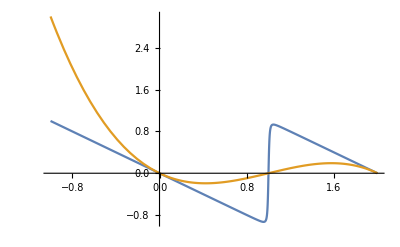

```mathematica
dy=0.01;
L0=1;
f1=-dx(1-L0/(√(dx^2+dy^2)))/.dx->(dx-L0);
f2=-dx/2(dx^2+dy^2-L0^2)/.dx->(dx-L0);
Plot[{f1,f2},{dx,-1,2}]
Clear[dy,L0]
```

```mathematica
f=(√(dx^2+dy^2)-L0)^2;
Series[f,{dy,0,2}]
```

(dx^2-2 √(dx^2) L0+L0^2)+(1-L0/(√(dx^2))) dy^2+O[dy]^3

```mathematica
meanPowerSpectrum[[1,1]]
```

(2 D1 dt (1-ⅇ^(-(2 dt k2)/γ)) γ (1-Cos[(2 k π)/M]))/(k2 (1+ⅇ^(-(2 dt k2)/γ)-2 ⅇ^(-(dt k2)/γ) Cos[(2 k π)/M]))